```mathematica
U0[ϵ_,UT_]:=UT/(1-ϵ)^(1/4)
x[ϵ_,UT_]:=Quiet[Sqrt[ϵ]/U0[ϵ,UT]^2*NIntegrate[1/Sqrt[((U/U0[ϵ,UT])^4-1+ϵ)*((U/U0[ϵ,UT])^4-1)],{U,U0[ϵ,UT],yy}]]
xtable[ϵ_,UT_]:=Join[Reverse[ParallelTable[{yy,x[ϵ,UT]},{yy,0,50,0.1}]],ParallelTable[{yy,-x[ϵ,UT]},{yy,0,50,0.1}]]
```

```mathematica
xtb01=xtable[0.0000001,1];
xtb0251=xtable[0.25,1];
xtb051=xtable[0.5,1];
xtb0751=xtable[0.75,1];
```

KernelConfiguration::cloudf: KernelConfiguration is not currently supported in the Wolfram Cloud.

KernelConfiguration::noker: Local is not a valid kernel specification.

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

```mathematica
UT1plt=ListLinePlot[{xtb01,xtb0251,xtb051,xtb0751},ScalingFunctions->{Identity,"Log"},ImageSize->Medium,AxesLabel->{"U","x/R^2"},PlotLabel->"UT=1",PlotLegends->{"ϵ~0","ϵ=0.25","ϵ=0.5","ϵ=0.75"}];
```

```mathematica
xtb03=xtable[0.0000001,3];
xtb0253=xtable[0.25,3];
xtb053=xtable[0.5,3];
xtb0753=xtable[0.75,3];
```

```mathematica
UT3plt=ListLinePlot[{xtb03,xtb0253,xtb053,xtb0753},ScalingFunctions->{Identity,"Log"},ImageSize->Medium,AxesLabel->{"U","x/R^2"},PlotLabel->"UT=3",PlotLegends->{"ϵ~0","ϵ=0.25","ϵ=0.5","ϵ=0.75"}];
```

```mathematica
xtb010=xtable[0.00001,10];
xtb02510=xtable[0.25,10];
xtb0510=xtable[0.5,10];
xtb07510=xtable[0.75,10];
```

```mathematica
UT10plt=ListLinePlot[{xtb010,xtb02510,xtb0510,xtb07510},ScalingFunctions->{Identity,"Log"},ImageSize->Medium,AxesLabel->{"U","x/R^2"},PlotLabel->"UT=10",PlotLegends->{"ϵ~0","ϵ=0.25","ϵ=0.5","ϵ=0.75"}];
```

```mathematica
Labeled[GraphicsRow[{UT1plt,UT3plt,UT10plt},ImageSize->Full],"String Configurations in an Ads BH"]
```

-Graphics-String Configurations in an Ads BH

```mathematica
(*also 8/15, can we get string configurations?*)
xvsUtb1={};
xvsUtb2={};
xvsUtb4={};
xvsUtb8={};
xvsUtb16={};
With[{UT=1},For[i=0,i<=2,i+=0.001,
UU=UT*10^i;
x=With[{U0=1.0001},Sqrt[1-(UT/U0)^4]/U0^2*Quiet[NIntegrate[1/Sqrt[((U/U0)^4-(UT/U0)^4)*((U/U0)^4-1)],{U,U0,UU/U0}]]];
x2=With[{U0=2},Sqrt[1-(UT/U0)^4]/U0^2*Quiet[NIntegrate[1/Sqrt[((U/U0)^4-(UT/U0)^4)*((U/U0)^4-1)],{U,U0,UU/U0}]]];
x4=With[{U0=4},Sqrt[1-(UT/U0)^4]/U0^2*Quiet[NIntegrate[1/Sqrt[((U/U0)^4-(UT/U0)^4)*((U/U0)^4-1)],{U,U0,UU/U0}]]];
x8=With[{U0=8},Sqrt[1-(UT/U0)^4]/U0^2*Quiet[NIntegrate[1/Sqrt[((U/U0)^4-(UT/U0)^4)*((U/U0)^4-1)],{U,U0,UU/U0}]]];
x16=With[{U0=16},Sqrt[1-(UT/U0)^4]/U0^2*Quiet[NIntegrate[1/Sqrt[((U/U0)^4-(UT/U0)^4)*((U/U0)^4-1)],{U,U0,UU/U0}]]];
AppendTo[xvsUtb1,{UU,x}];
AppendTo[xvsUtb2,{UU,x2}];
AppendTo[xvsUtb4,{UU,x4}];
AppendTo[xvsUtb8,{UU,x8}];
AppendTo[xvsUtb16,{UU,x16}];
]]
xvsUtb1=Drop[xvsUtb1,1];
```

```mathematica
xvsUtb12=Join[Reverse[xvsUtb1],Transpose[{xvsUtb1[[All,1]],-xvsUtb1[[All,2]]}]];
xvsUtb22=Join[Reverse[xvsUtb2],Transpose[{xvsUtb2[[All,1]],-xvsUtb2[[All,2]]}]];
xvsUtb42=Join[Reverse[xvsUtb4],Transpose[{xvsUtb4[[All,1]],-xvsUtb4[[All,2]]}]];
xvsUtb82=Join[Reverse[xvsUtb8],Transpose[{xvsUtb8[[All,1]],-xvsUtb8[[All,2]]}]];
xvsUtb162=Join[Reverse[xvsUtb16],Transpose[{xvsUtb16[[All,1]],-xvsUtb16[[All,2]]}]];
```

```mathematica
ListLinePlot[{xvsUtb12,xvsUtb22,xvsUtb42,xvsUtb82,xvsUtb162},ScalingFunctions->"SignedLog",PlotLabels->{"rm~r0","rm=2r0","rm=4r0","rm=8r0","rm=16r0"},AxesLabel->{"r","x/L^2"},PlotLabel->"String Configurations in an  AdsBH Spacetime",ImageSize->Large]
```

-Graphics-

```mathematica
(*ok so i dont wanna fight with getting the tables flipped so the bottom half also matches at the moment but this is nice*)
```

```mathematica
(*8/15/24. Gonna try and use tables better / more from here on out*)
```

```mathematica
U0vsLtb={};
With[{UT=1},For[i=0.0001,i<=2,i+=0.05,
U0=10^i;
L=(2*Sqrt[1-(UT/U0)^4])/U0 NIntegrate[1/Sqrt[(y^4-(UT/U0)^4)*(y^4-1)],{y,1,Infinity}];
AppendTo[U0vsLtb,{U0,L}]
]]
```

```mathematica
U0vsLtb
```

{{1.00023,0.134807},{1.12228,0.857779},{1.25922,0.855322},{1.41286,0.799067},{1.58526,0.729754},{1.77869,0.65943},{1.99572,0.592537},{2.23924,0.530723},{2.51246,0.474454},{2.81903,0.423662},{3.16301,0.378037},{3.54895,0.337177},{3.98199,0.30065},{4.46786,0.268034},{5.01303,0.23893},{5.62471,0.212971},{6.31103,0.189825},{7.08109,0.169189},{7.94511,0.150795},{8.91456,0.134398},{10.0023,0.119784},{11.2228,0.106758},{12.5922,0.095149},{14.1286,0.0848019},{15.8526,0.0755799},{17.7869,0.0673607},{19.9572,0.0600354},{22.3924,0.0535066},{25.1246,0.0476878},{28.1903,0.0425018},{31.6301,0.0378798},{35.4895,0.0337604},{39.8199,0.030089},{44.6786,0.0268168},{50.1303,0.0239005},{56.2471,0.0213014},{63.1103,0.0189849},{70.8109,0.0169203},{79.4511,0.0150802},{89.1456,0.0134403}}

```mathematica
(*ok that was nice, now w energy*)
```

```mathematica
EvsLtb={};
With[{UT=1},For[i=0,i<=2,i+=0.01,
U0=UT*10^i;
L=(2*Sqrt[1-(UT/U0)^4])/U0 NIntegrate[1/Sqrt[(y^4-(UT/U0)^4)*(y^4-1)],{y,1,Infinity}];
delE=U0/Pi*NIntegrate[Sqrt[(y^4-(UT/U0)^4)/(y^4-1)]-1,{y,1,Infinity}]-U0/Pi+UT/Pi;
AppendTo[EvsLtb,{L,delE}]
]]
EvsLtb=Drop[EvsLtb,4];
coulombtable=Table[{x,-0.2/x},{x,0.01,1,0.01}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.0000000000000000000000000000163072643374912722470619778528907452}. NIntegrate obtained 37.1739 and 5.81182 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

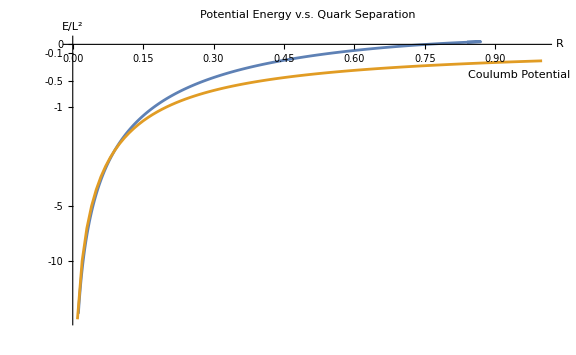

```mathematica
ListLinePlot[{EvsLtb,coulombtable},ScalingFunctions->{Identity,"SignedLog"},PlotLabel->"Potential Energy v.s. Quark Separation", PlotLabels->Placed[{"String Potential","Coulumb Potential"},Right],ImageSize->Large,AxesLabel->{"R","E/L^2"}]
```

```mathematica
EvsLtb2={};
With[{UT=0.0001},For[i=0,i<=7,i+=0.1,
U0=UT*10^i;
L=(2*Sqrt[1-(UT/U0)^4])/U0 NIntegrate[1/Sqrt[(y^4-(UT/U0)^4)*(y^4-1)],{y,1,Infinity}];
delE=U0/Pi*NIntegrate[Sqrt[(y^4-(UT/U0)^4)/(y^4-1)]-1,{y,1,Infinity}]-U0/Pi+UT/Pi;
AppendTo[EvsLtb2,{L,delE}]
]]
EvsLtb2=Drop[EvsLtb2,1];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.0000000000000016644770259844551249359338633789390246300689292285}. NIntegrate obtained 8.90425 and 0.364036 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
coulombtable2=Table[{x,-0.1/x},{x,0,10000,1}];
```

Power::infy: Infinite expression 1/0 encountered.

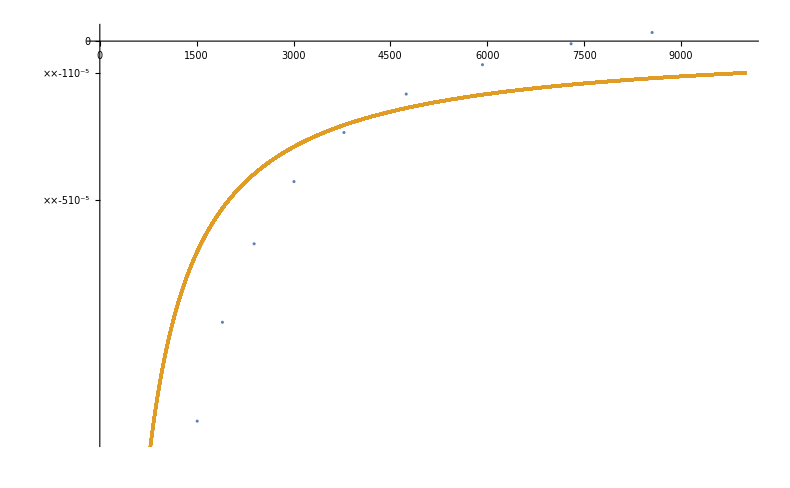

```mathematica
ListPlot[{EvsLtb2,coulombtable2},ScalingFunctions->"SignedLog",PlotRange->Automatic]
```

```mathematica
(*so ive been looking trying to find some kind of phase transition for different UT (effectively temperature right), where dele would all of a sudden behave like a coulomb. i dont think I'll find this anymore, the last paragraphs of the paper make me think that there isnt a temperature dependent phase transition here. obviously for different quark separations we get different potential curves, but i dont think the whole shape of the curve will change above or below some temperature*)
```